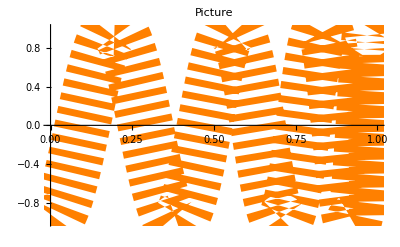

```mathematica
f[x_]:= 1 -2*x^2
Plot[f[f[f[f[x]]]], {x,0,1}, PlotLabel->"Picture", PlotStyle->{Dashed, Orange, Thickness[0.1]}]
```

```mathematica
Plot3D[Sin[x/(y+Pi/10)], {x,0,2*Pi},{y,0,Pi/2},PlotPoints -> 40, AxesLabel -> {"X","Y","Z"}]
```

-Graphics3D-

```mathematica
Solve[Log[x+Sqrt[x^2+a]]== b, x]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→1/2 ⅇ^-b (-a+ⅇ^(2 b))}}

```mathematica
Solve[x^4 - 5*x^2 -3 ==0 , x]
```

{{x→-ⅈ √(1/2 (-5+√37))},{x→ⅈ √(1/2 (-5+√37))},{x→-√(1/2 (5+√37))},{x→√(1/2 (5+√37))}}

```mathematica
Solve[Cos[x]==Tan[x]&& 0<=x<2*Pi,x]
```

{{x→2 ArcTan[]},{x→2 ArcTan[]}}

```mathematica
Solve[Log[Sqrt[x]]== Sqrt[Log[x]], x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1},{x→ⅇ^4}}

```mathematica
Solve[x^3 - 3x -1 ==0, x]
```

{{x→},{x→},{x→}}

```mathematica
Solve[a*x^4 +b*x^3 +1 == 0, x]
```

{{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))}}

```mathematica
NSolve[x^7 +7x == 7,x]
NSolve[Cos[x]== x,x]
```

{{x→-1.3217-0.706695 ⅈ},{x→-1.3217+0.706695 ⅈ},{x→-0.137797-1.43289 ⅈ},{x→-0.137797+1.43289 ⅈ},{x→0.920191},{x→0.999402-0.797172 ⅈ},{x→0.999402+0.797172 ⅈ}}

{{x→0.739085},{x→-2.48689+1.80936 ⅈ},{x→-9.10999+2.95017 ⅈ},{x→-15.488+3.45661 ⅈ},{x→-21.819+3.79031 ⅈ},{x→-28.1316+4.03995 ⅈ},{x→-34.435+4.23954 ⅈ},{x→-40.7329+4.40585 ⅈ},{x→-47.0274+4.54842 ⅈ},{x→-53.3196+4.67319 ⅈ},{x→-59.6102+4.78411 ⅈ},{x→-65.8995+4.88396 ⅈ},{x→-72.1878+4.97474 ⅈ},{x→-78.4754+5.05797 ⅈ},{x→-84.7625+5.1348 ⅈ},{x→-91.0491+5.20615 ⅈ}}

```mathematica
FindRoot[Exp[x] == x^2, {x, -1}]
```

{x→-0.703467}

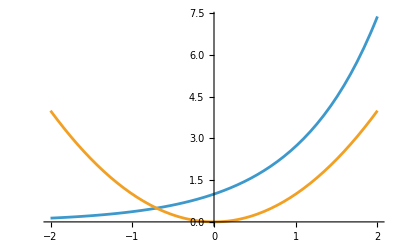

```mathematica
Plot[{Exp[x],x^2}, {x, -2, 2}]
```

```mathematica
FindRoot[Sinh[x] == 1 + 1/x, {x, {-2, 1}}]
```

{x→{-0.607635,1.32752}}

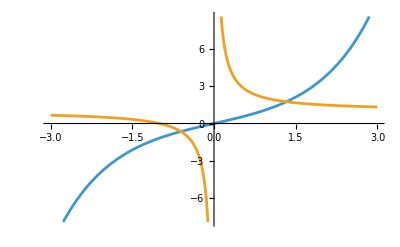

```mathematica
Plot[{Sinh[x], 1 + 1/x}, {x, -3, 3}, Exclusions -> {x ==0}]
```

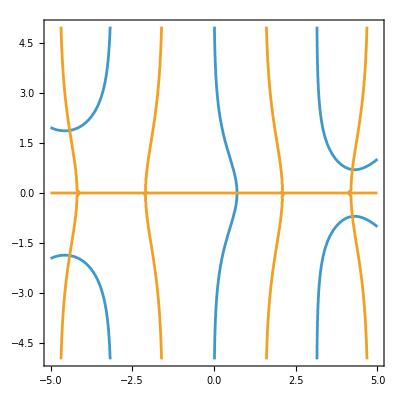

```mathematica
ContourPlot[{Re[Sin[x + I*y]] == Re[1 - (x + I*y)/2], Im[Sin[x + I*y]] == Im[1 - (x + I*y)/2]},{x, -5, 5}, {y, -5,5}]
```

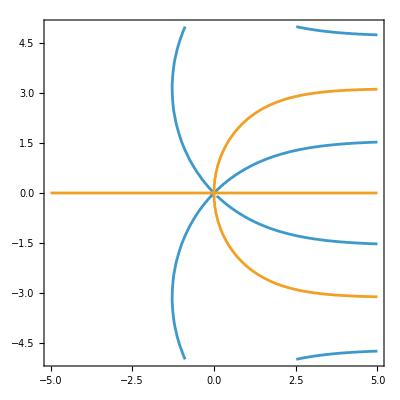

```mathematica
ContourPlot[{Re[Exp[x+I*y]]==Re[(x+I*y)+1],Im[Exp[x+I*y]]==Im[(x+I*y)+1]},{x,-5,5},{y,-5,5}]
```

```mathematica
sol1 = Solve[{x+y == 5, x -y ==1}, {x,y} ]
```

{{x→3,y→2}}

```mathematica
{x+y==5, x-y ==1}/.sol1
```

{{True,True}}

```mathematica
NSolve[{Sqrt[x+y]==Sqrt[x*y],x^2-y^2==1},{x,y}]
```

{{x→2.13224,y→1.8832},{x→-1.13224,y→0.53101},{x→0.5+0.405233 ⅈ,y→-0.207107-0.978318 ⅈ},{x→0.5-0.405233 ⅈ,y→-0.207107+0.978318 ⅈ}}

```mathematica
NSolve[{Sin[x+y]==Cos[x-y],Tan[x*y]==Cos[x*y],-5<x<5,-5<y<5},{x,y}]
```

{{x→-4.84828,y→0.785398},{x→-4.63034,y→3.92699},{x→-4.16966,y→3.92699},{x→-3.71724,y→-2.35619},{x→-3.03034,y→3.92699},{x→-2.94943,y→-2.35619},{x→-2.56966,y→3.92699},{x→-2.35619,y→-0.282761},{x→-2.35619,y→-1.05057},{x→-2.35619,y→4.28276},{x→-2.35619,y→-3.71724},{x→-2.35619,y→1.61609},{x→-2.35619,y→-2.94943},{x→-2.35619,y→2.38391},{x→-1.43034,y→3.92699},{x→-1.05057,y→-2.35619},{x→-0.969656,y→3.92699},{x→-0.282761,y→-2.35619},{x→0.169656,y→3.92699},{x→0.630344,y→3.92699},{x→0.785398,y→0.848282},{x→0.785398,y→-4.84828},{x→0.785398,y→3.15172},{x→0.848282,y→0.785398},{x→1.61609,y→-2.35619},{x→1.76966,y→3.92699},{x→2.23034,y→3.92699},{x→2.38391,y→-2.35619},{x→3.15172,y→0.785398},{x→3.36966,y→3.92699},{x→3.83034,y→3.92699},{x→3.92699,y→-3.03034},{x→3.92699,y→0.169656},{x→3.92699,y→3.36966},{x→3.92699,y→-2.56966},{x→3.92699,y→0.630344},{x→3.92699,y→3.83034},{x→3.92699,y→-4.16966},{x→3.92699,y→-0.969656},{x→3.92699,y→2.23034},{x→3.92699,y→-4.63034},{x→3.92699,y→-1.43034},{x→3.92699,y→1.76966},{x→3.92699,y→4.96966},{x→4.28276,y→-2.35619},{x→4.96966,y→3.92699}}

```mathematica
a=Eliminate[{x^2+y^2-z^2==1,x+y==z,Sinh[z]==x^2+y^2},{x,y}]

b=FindRoot[a,{z,3}]

FindRoot[{x^2+y^2-z^2==1,x+y==z}/. b,{x,1},{y,2}]
```

1+z^2-Sinh[z]==0

{z→2.99559}

{x→-0.158523,y→3.15411}

```mathematica
DSolve[y''[x]*x^2 +5y'[x]*x +y[x]== 0,y[x], x]
```

{{y[x]→x^(1/2 (-4-2 √3)) C[1]+x^(1/2 (-4+2 √3)) C[2]}}

```mathematica
DSolve[y''[x]*x^2+3*y'[x]*x+y[x]== Sin[2*x], y[x], x]
```

{{y[x]→C[1]/x-CosIntegral[2 x]/(2 x)+(C[2] Log[x])/x}}

```mathematica
DSolve[{y''[x]*x^2+5*y'[x]*x+y[x]==x^(-2+Sqrt[3]),y[1]==-1/12,y'[1]==1/12*(2+Sqrt[3])},y[x],x]
```

{{y[x]→1/12 x^(-2+√3) (-1+2 √3 Log[x])}}

```mathematica
DSolve[y''[x]+y[x]/Sin[x]^2 == 0, y[x],x]
```

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[-1/2,(ⅈ √3)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[-1/2,(ⅈ √3)/2,Cos[x]]}}

```mathematica
DSolve[{x'[t]==t^2+y[t],y'[t]==x[t]},{x[t],y[t]},t]
```

{{x[t]→1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t)) (-2-2 t-t^2-ⅇ^(2 t) (2-2 t+t^2))+1/4 ⅇ^(-2 t) (1+ⅇ^(2 t)) (-2-2 t-t^2+ⅇ^(2 t) (2-2 t+t^2))+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→1/4 ⅇ^(-2 t) (1+ⅇ^(2 t)) (-2-2 t-t^2-ⅇ^(2 t) (2-2 t+t^2))+1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t)) (-2-2 t-t^2+ⅇ^(2 t) (2-2 t+t^2))+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
DSolve[{y''[t]==4*x[t]-5*y[t],x''[t]==4*y[t]-5*x[t],y[0]==1,x[0]==0,y'[0]==0,x'[0]==1},{x[t],y[t]},t]
```

{{x[t]→1/6 (3 Cos[t]-3 Cos[3 t]+3 Sin[t]+Sin[3 t]),y[t]→1/6 (3 Cos[t]+3 Cos[3 t]+3 Sin[t]-Sin[3 t])}}

```mathematica
Clear[x,t];
```

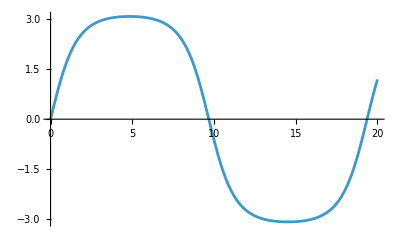

```mathematica
sol=NDSolve[{x''[t]==-Sin[x[t]],x[0]==0,x'[0]==1.999},x,{t,0,20}];
Plot[Evaluate[x[t]/. sol],{t,0,20}]
```